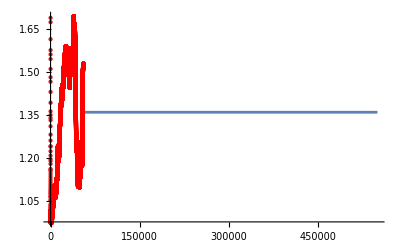

```mathematica
(* Read atmospheric 14C data*)
SetDirectory["/Users/yinonmb/Weizmann Institute Dropbox/YinonMoise Bar-On/git/soil_diskin/notebooks"];
C14DATADIR="../data/14C_atm_annot.csv";
C14DATA=Import[C14DATADIR, "HeaderLines"-> 1];
C14DATA= C14DATA[[All,{4,5}]];
(*Interpolate the 14C data, use the mean ratio for extrapolation*)
MeanR = Last[Mean[C14DATA[[-50000;;]]]];
atm14C=Interpolation[C14DATA,InterpolationOrder->0,"ExtrapolationHandler"-> {(MeanR&)}];

(* Plot the results of the interpolation to see it makes sense *)
Plot[atm14C[x],{x,0,550000},Epilog->{PointSize[Medium],Red,Point[C14DATA]}]
```

```mathematica
(* Define the function that calculatehe
LognormalRadiocarbon[tau_,age_] := (
sig = Sqrt[Log[age/tau]];
mu = -Log[Sqrt[tau^3/age]];
r = NIntegrate[ atm14C[a]*Exp[-a/8267]* PDF[LogNormalDistribution[mu,sig],x] * Exp[-x*a] / Exp[-mu+(sig^2)/2],{x,0,Infinity},{a,0,Infinity}];
r
)
```

```mathematica
FindOptimalAge[tau_?NumericQ,rtrue_?NumericQ,InitialAge_?NumericQ]:=Module[{objectiveFunction,solution},(*Define the objective function to minimize:the squared difference between the function output and r_true*)objectiveFunction[age_?NumericQ]:=(LognormalRadiocarbon[tau,age]-rtrue)^2;
(*Use FindMinimum to find the age that minimizes the objective function*)(*FindMinimum requires a starting point for'age'*)solution=Quiet[FindMinimum[objectiveFunction[age],{age,InitialAge}]];
(*Return the value of age that minimizes the difference*)Return[age/. Last[solution]]]

tauExample=50; (*Replace with your desired tau value*)
rTrueExample=0.9; (*Replace with your observed r_true value*)
ageInitialExample=100; (*An initial guess for age*)

(*Call the function to find the optimal age*)
optimalAgeFound=FindOptimalAge[tauExample,rTrueExample,ageInitialExample]
```

```mathematica
5490.080428081148

LognormalRadiocarbon[50,5490.080428081148]
```

5490.08

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.9 and 0.000555001 for the integral and error estimates.

0.9

```mathematica
FindOptimalAge[tau_?NumberQ,rtrue_?NumberQ]:=((*Method 2:Using NMinimize to minimize the squared difference*)(*This method is more robust as it minimizes a cost function and doesn't require the function to be monotonic or have an exact root.*)Print["Attempting to find optimal age using NMinimize..."];
objectiveFunction[age2_?NumberQ]:=(LognormalRadiocarbon[tau,age2]-rtrue)^2;
(*Set a reasonable search range for'age'.Adjust as needed based on your problem.*)ageMin=1;(*Example minimum age*)ageMax=100000;(*Example maximum age*)optimalAgeNMinimize=NMinimize[objectiveFunction[age],{age,ageMin,ageMax}];
Print["NMinimize Result: ",optimalAgeNMinimize];
optimalAgeNMinimize
)

(*Example Usage:*)
tauExample=50; (*Replace with your desired tau value*)
rTrueExample=0.9; (*Replace with your observed r_true value*)
ageInitialExample=100; (*An initial guess for age*)

(*Call the function to find the optimal age*)
optimalAgeFound=FindOptimalAge[tauExample,rTrueExample]

Print["The optimal 'age' parameter is approximately: ",optimalAgeFound];
```

Attempting to find optimal age using NMinimize...

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.869371 and 0.000562838 for the integral and error estimates.

LogNormalDistribution::posprm: Parameter 0.+1.97024 ⅈ at position 2 in LogNormalDistribution[-5.85294,0.+1.97024 ⅈ] is expected to be positive.

NIntegrate::inumr: The integrand (0.02+0. ⅈ) ⅇ^(-a/8267-a x) PDF[LogNormalDistribution[-5.85294,0.+1.97024 ⅈ],x] InterpolatingFunction[{{-13.,55050.}},{5,7,0,{55064},{1},0,0,0,0,MeanR&,«3»},{{-13.,-12.,-11.,-10.,-9.,-8.,-7.,-6.,-5.,-4.,«55054»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«55055»},{1.0193,1.0222,1.02665,1.03017,1.03416,1.03868,1.0515,1.05515,1.0649,1.064,«55054»}},{Automatic}][a] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.,0.},{∞,0.}}.

LogNormalDistribution::posprm: Parameter 0.+1.97024 ⅈ at position 2 in LogNormalDistribution[-5.85294,0.+1.97024 ⅈ] is expected to be positive.

NIntegrate::inumr: The integrand (0.02+0. ⅈ) ⅇ^(-a/8267-a x) PDF[LogNormalDistribution[-5.85294,0.+1.97024 ⅈ],x] InterpolatingFunction[{{-13.,55050.}},{5,7,0,{55064},{1},0,0,0,0,MeanR&,«3»},{{-13.,-12.,-11.,-10.,-9.,-8.,-7.,-6.,-5.,-4.,«55054»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«55055»},{1.0193,1.0222,1.02665,1.03017,1.03416,1.03868,1.0515,1.05515,1.0649,1.064,«55054»}},{Automatic}][a] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.,0.},{∞,0.}}.

LogNormalDistribution::posprm: Parameter 0.+1.97024 ⅈ at position 2 in LogNormalDistribution[-5.85294,0.+1.97024 ⅈ] is expected to be positive.

General::stop: Further output of LogNormalDistribution::posprm will be suppressed during this calculation.

NIntegrate::inumr: The integrand (0.02+0. ⅈ) ⅇ^(-a/8267-a x) PDF[LogNormalDistribution[-5.85294,0.+1.97024 ⅈ],x] InterpolatingFunction[{{-13.,55050.}},{5,7,0,{55064},{1},0,0,0,0,MeanR&,«3»},{{-13.,-12.,-11.,-10.,-9.,-8.,-7.,-6.,-5.,-4.,«55054»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«55055»},{1.0193,1.0222,1.02665,1.03017,1.03416,1.03868,1.0515,1.05515,1.0649,1.064,«55054»}},{Automatic}][a] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.,0.},{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NMinimize::nnum: The function value (-0.9+NIntegrate[(atm14C[a] Exp[-a/8267] PDF[LogNormalDistribution[mu,sig],x] Exp[«2» a])/Exp[Plus[«2»]],{x,0,∞},{a,0,∞}])^2 is not a number at {age} = {1.03065}.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.869371 and 0.000562838 for the integral and error estimates.

NMinimize::nnum: The function value (-0.9+NIntegrate[(atm14C[a] Exp[-a/8267] PDF[LogNormalDistribution[mu,sig],x] Exp[«2» a])/Exp[Plus[«2»]],{x,0,∞},{a,0,∞}])^2 is not a number at {age} = {1.03065}.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.869371 and 0.000562838 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NMinimize::nnum: The function value (-0.9+NIntegrate[(atm14C[a] Exp[-a/8267] PDF[LogNormalDistribution[mu,sig],x] Exp[«2» a])/Exp[Plus[«2»]],{x,0,∞},{a,0,∞}])^2 is not a number at {age} = {1.03065}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

NMinimize Result: NMinimize[objectiveFunction[age],{age,1,100000}]

NMinimize[objectiveFunction[age],{age,1,100000}]

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.869371 and 0.000562838 for the integral and error estimates.

LogNormalDistribution::posprm: Parameter 0.+1.97024 ⅈ at position 2 in LogNormalDistribution[-5.85294,0.+1.97024 ⅈ] is expected to be positive.

NIntegrate::inumr: The integrand (0.02+0. ⅈ) ⅇ^(-a/8267-a x) PDF[LogNormalDistribution[-5.85294,0.+1.97024 ⅈ],x] InterpolatingFunction[{{-13.,55050.}},{5,7,0,{55064},{1},0,0,0,0,MeanR&,«3»},{{-13.,-12.,-11.,-10.,-9.,-8.,-7.,-6.,-5.,-4.,«55054»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«55055»},{1.0193,1.0222,1.02665,1.03017,1.03416,1.03868,1.0515,1.05515,1.0649,1.064,«55054»}},{Automatic}][a] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.,0.},{∞,0.}}.

LogNormalDistribution::posprm: Parameter 0.+1.97024 ⅈ at position 2 in LogNormalDistribution[-5.85294,0.+1.97024 ⅈ] is expected to be positive.

NIntegrate::inumr: The integrand (0.02+0. ⅈ) ⅇ^(-a/8267-a x) PDF[LogNormalDistribution[-5.85294,0.+1.97024 ⅈ],x] InterpolatingFunction[{{-13.,55050.}},{5,7,0,{55064},{1},0,0,0,0,MeanR&,«3»},{{-13.,-12.,-11.,-10.,-9.,-8.,-7.,-6.,-5.,-4.,«55054»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«55055»},{1.0193,1.0222,1.02665,1.03017,1.03416,1.03868,1.0515,1.05515,1.0649,1.064,«55054»}},{Automatic}][a] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.,0.},{∞,0.}}.

LogNormalDistribution::posprm: Parameter 0.+1.97024 ⅈ at position 2 in LogNormalDistribution[-5.85294,0.+1.97024 ⅈ] is expected to be positive.

General::stop: Further output of LogNormalDistribution::posprm will be suppressed during this calculation.

NIntegrate::inumr: The integrand (0.02+0. ⅈ) ⅇ^(-a/8267-a x) PDF[LogNormalDistribution[-5.85294,0.+1.97024 ⅈ],x] InterpolatingFunction[{{-13.,55050.}},{5,7,0,{55064},{1},0,0,0,0,MeanR&,«3»},{{-13.,-12.,-11.,-10.,-9.,-8.,-7.,-6.,-5.,-4.,«55054»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«55055»},{1.0193,1.0222,1.02665,1.03017,1.03416,1.03868,1.0515,1.05515,1.0649,1.064,«55054»}},{Automatic}][a] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.,0.},{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NMinimize::nnum: The function value (-0.9+NIntegrate[(atm14C[a] Exp[-a/8267] PDF[LogNormalDistribution[mu,sig],x] Exp[«2» a])/Exp[Plus[«2»]],{x,0,∞},{a,0,∞}])^2 is not a number at {age} = {1.03065}.

The optimal 'age' parameter is approximately: NMinimize[objectiveFunction[age],{age,1,100000}]

```mathematica
FindOptimalAge[50,0.9,100]
```

FindOptimalAge[50,0.9,100]

InterpolatingFunction::dmval: Input value {-500000} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
atm14C[2]
```

1.09443